```mathematica
Clear["Global`*"]
```

```mathematica
EulerLagrangeEquations[L_,vars_List]:=MapThread[(D[D[L, (D[#, t])], t]==D[L, #])&,{vars}]
```

```mathematica
ℒ=1/2 m(r'[t]^2+(r[t]+L)^2 θ'[t]^2)-1/2 k r[t]^2-m g (r[t]+L)(1-Cos[θ[t]]);
```

```mathematica
eqs=EulerLagrangeEquations[ℒ,{r[t],θ[t]}]
ic={r[0]==0.8,r'[0]==0,θ[0]==Pi/12,θ'[0]==0};(*CONDIÇÕES INICIAS*)
params={L-> 0.5,g-> 9.82,m->4,k->1};(*PARAMETROS*)
TMAX=30;
```

{m r''[t]==-g m (1-Cos[θ[t]])-k r[t]+m (L+r[t]) θ'[t]^2,2 m (L+r[t]) r'[t] θ'[t]+m (L+r[t])^2 θ''[t]==-g m (L+r[t]) Sin[θ[t]]}

```mathematica
sol=NDSolve[{eqs,ic}/.params,{r[t],θ[t]},{t,0,TMAX}]//Flatten;
```

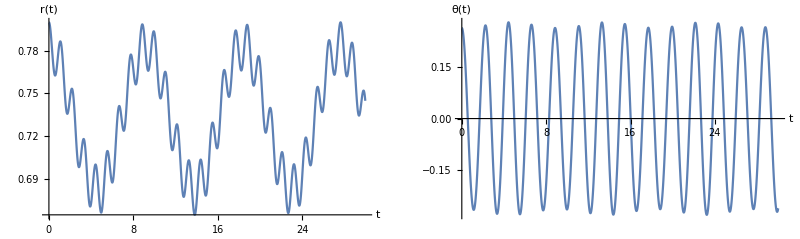

```mathematica
{{
Plot[r[t]/.sol,{t,0,30},ImageSize->400,
AxesLabel->MapThread[Style[#,FontColor->Black,FontWeight->Bold,FontSize->14]&,{{t,r[t]}}]
],
Plot[Evaluate[θ[t]/.sol],{t,0,TMAX},ImageSize->400,
AxesLabel->MapThread[Style[#,FontColor->Black,FontWeight->Bold,FontSize->14]&,{{t,θ[t]}}]
]
}}//GraphicsGrid
```

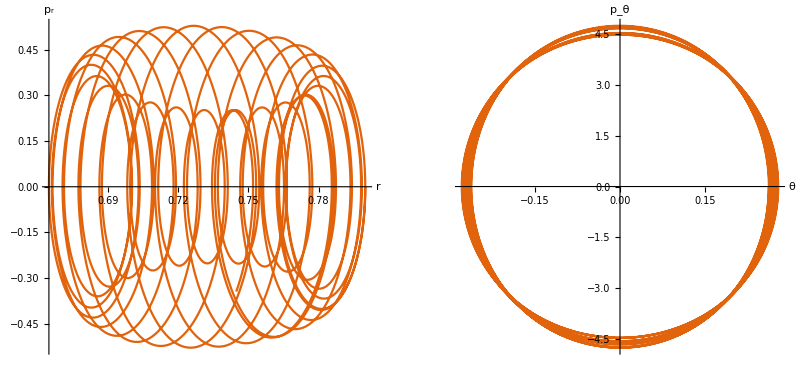

```mathematica
{{
ParametricPlot[Evaluate[{r[t]/.sol,D[(m r[t]/.sol), t]}/.params],{t,0,TMAX},
ImageSize->400,AspectRatio->1,ColorFunction->(ColorData["SolarColors"][#3]&),
AxesLabel->MapThread[Style[#,FontColor->Black,FontWeight->Bold,FontSize->14]&,{{r,Subscript[p, r]}}]],
ParametricPlot[Evaluate[{θ[t],m (r[t]+L)^2 D[( θ[t]/.sol), t]}/.sol/.params],{t,0,TMAX},
ImageSize->400,AspectRatio->1,PlotRange->All,ColorFunction->(ColorData["SolarColors"][#3]&),AxesLabel->MapThread[Style[#,FontColor->Black,FontWeight->Bold,FontSize->14]&,{{θ,Subscript[p, θ]}}]]
}}//GraphicsGrid
```

```mathematica
pos[t_]:=Evaluate[(r[t]+L)*{Sin[θ[t]],-Cos[θ[t]]}/.sol/.params];
```

```mathematica
{minX,minY}=MinValue[{#,0≤t≤TMAX},t]&/@pos[t];
{maxX,maxY}=MaxValue[{#,0≤t≤TMAX},t]&/@pos[t];
Animate[Graphics[{
{White,Rectangle[1.2*Floor@{minX, minY},1.2*Ceiling@{maxX, Max[maxY,0]}]},
{Blue,Thickness[0.005],Line[{{0,0},pos[t]}]},
{Black,Disk[pos[t],0.08]}
}],{t,0,TMAX},AnimationRate->1]
```